```mathematica
Graph[Table[i->Mod[i^2, 37], {i, 100}]]
```

-Graphics-

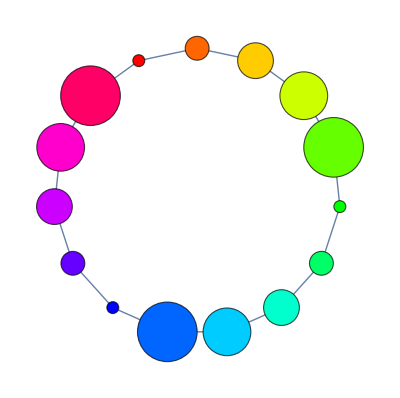

```mathematica
Graph[Table[Annotation[v, {VertexSize->0.2+0.2Mod[v, 5], VertexStyle->Hue[v/15,1,1]}], {v,0,14}],Table[v<->Mod[v+1,15],{v,0,14}]]
```

```mathematica
g0 = Graph[{1<->2, 2<->3,3<->1}, EdgeWeight->{2,8,14}];
shapeFunc = With[{weight=AnnotationValue[{g, #2}, EdgeWeight]},{AbsoluteThickness[weight], Line[#1]}] &;
Graph[g, EdgeShapeFunction ->shapeFunc]
(*
(With[{weight=AnnotationValue[{g,#2},EdgeWeight]},{AbsoluteThickness[weight],Line[#1]}]&)
[{{-0.8660254037844384,-0.49999999999999933},{1.8369701987210297*^-16,1.}},1<->2]
*)
```

Graph[g,EdgeShapeFunction→(With[{weight=AnnotationValue[{g,#2},EdgeWeight]},{AbsoluteThickness[weight],Line[#1]}]&)]

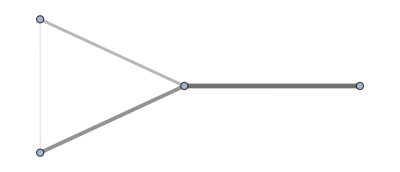

```mathematica
g = Graph[{1<->2, 2<->3,3<->1, 4<->3}, EdgeWeight->{2,8,16,30}];
weightFunc[w_] := If[w < 5, 0.8, If[w<15, 0.6, If[w < 25, 0.4, If[w < 50, 0.2, 0.0]]]];
shapeFunc = With[{weight=AnnotationValue[{g, #2}, EdgeWeight]},{AbsoluteThickness[Log[weight]], Hue[0, 0, weightFunc[weight]], Line[#1]}] &;
Graph[g, EdgeShapeFunction ->shapeFunc]
```

```mathematica
SetDirectory["C:/Users/hojun/Desktop/Wolfram Mathematica"];
Directory[]
```

C:\Users\hojun\Desktop\Wolfram Mathematica

```mathematica
tStr = Import["input.txt", "Text"]
```

a b 2
b c 8
c d 16
d e 30
a e 22
b e 52

```mathematica
tStlines =Map[With[{line=#}, StringSplit[line]]&,StringSplit[tStr, "\n"]]
```

{{a,b,2},{b,c,8},{c,d,16},{d,e,30},{a,e,22},{b,e,52}}

```mathematica
linkList = {};
Do[linkList = Append[linkList, i[[1]]<->i[[2]]],{i, tStlines}];
linkList
```

{a<->b,b<->c,c<->d,d<->e,a<->e,b<->e}

```mathematica
weightList = {};
Do[weightList=Append[weightList,Interpreter["Number"][i[[3]]]],{i,tStlines}];
weightList
```

{2,8,16,30,22,52}

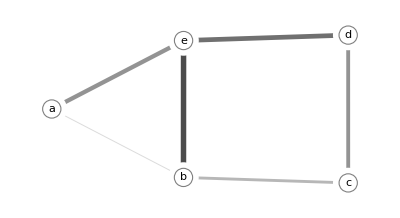

```mathematica
Datag =Graph[linkList,EdgeWeight->weightList];
weightFunc[w_] := If[w < 5, 0.8, If[w<15, 0.6, If[w < 25, 0.4, If[w < 50, 0.2, 0.0]]]];
shapeFunc = With[{weight=AnnotationValue[{Datag, #2}, EdgeWeight]},{AbsoluteThickness[Log[weight]], Hue[0, 0, weightFunc[weight]], Line[#1]}] &;
Graph[Datag, EdgeShapeFunction ->shapeFunc, VertexLabels->Placed[Automatic, Center], VertexLabelStyle->Black, VertexShapeFunction->({EdgeForm[None], White,Disk[#1,.1],EdgeForm[Gray], White, Disk[#1, .06]}&)]
```